```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/m0/m0_500/midmub

```mathematica
dataall=Table[Import["../../Shi_middle_mu_B/Shi_mu="<>ToString[i]<>"_m0=500.0-flag_4-51x104_VC=true.csv"],{i,800,960,5}];
```

```mathematica
n=Length[Table[i,{i,800,960,5}]]
```

33

```mathematica
dataall[[1]]
```

```mathematica
pdata=Table[Table[Table[dataall[[n1]][[j*104+i]][[5]],{i,2,105}],{j,0,50}],{n1,1,33}];
```

```mathematica
Table[Table[Export["./mub"<>ToString[(i-1)*5+800]<>"/V"<>ToString[j]<>".dat",pdata[[i]][[j]]],{i,1,33}],{j,1,51}];
```

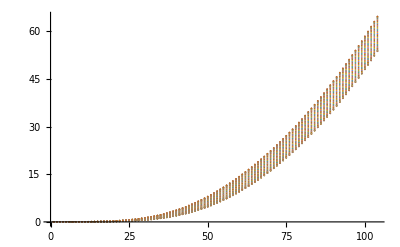

```mathematica
ListPlot[pdata[[1]]]
```